# Simu data

## Load data

### Interaction data

```mathematica
Options[WeightedHistogram]=Append[Options[Histogram],"SampleSize"->1000];

WeightedHistogram[weights_->values_,o:OptionsPattern[]]:=WeightedHistogram[weights->values,Automatic,o]

WeightedHistogram[weights_->values_,bins_,o:OptionsPattern[]]:=Block[{sample,newbins,valuelists,partitions},sample=Join[RandomChoice[weights->values,OptionValue["SampleSize"]],values];
newbins=First[HistogramList[sample,bins]];
partitions=Partition[newbins,2,1];
valuelists=Total[Pick[weights,Thread[#≤values<#2]]]&@@@partitions;
Histogram[values,{newbins},valuelists&,FilterRules[Flatten[{o}],Options[Histogram]]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*SetDirectory["/home/miglesia/Documents/IST"];*)
files=FileNames["*.csv"]
fl=Length[files];
import1=Table[ImportString[StringReplace[Import[files[[m]],"Text"],{";"->","}],"CSV"],{m,1,fl}];
```

{EMI-simulation-2016-03-23_00-39-47.csv,EMI-simulation-2016-03-23_00-58-23.csv,EMI-simulation-2016-03-23_01-25-27.csv,EMI-simulation-2016-03-23_15-17-35.csv}

```mathematica
simu=Table[DeleteDuplicates[import1[[f,2;;-1,1]]],{f,1,fl}];
nl=Table[Length[simu[[f]]],{f,1,fl}];
parts=Table[Table[Flatten[Position[import1[[f,2;;-1,1]],_?(#==n&)]],{n,1,nl[[f]]}],{f,1,fl}];
data=Table[Table[import1[[f,2;;-1]][[parts[[f,n]]]],{n,1,nl[[f]]}],{f,1,fl}];badruns=Table[Position[Table[data[[f,n,-1,3]],{n,1,nl[[f]]}],_?(#>1*^6 &)],{f,1,fl}]
dataf=Table[,{f,1,fl}];
Do[dataf[[f]]=Delete[data[[f]],badruns[[f]]],{f,1,fl}];
nl=Table[Length[dataf[[f]]],{f,1,fl}];
p=Table[Round[Length[dataf[[f]]]/2],{f,1,fl}];
len=Table[Length[dataf[[f,1]]],{f,1,fl}];
```

{{},{},{},{}}

### Plot Titles

```mathematica
info={"μ=0.3","μ=0.6","μ=1.2","μ=1.5"};
```

```mathematica
dataf//Dimensions
```

{4}

### Bankrupcy frequency

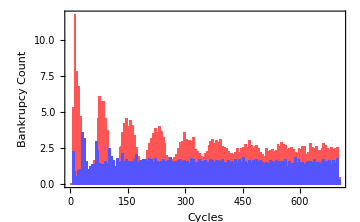
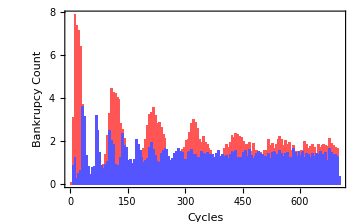
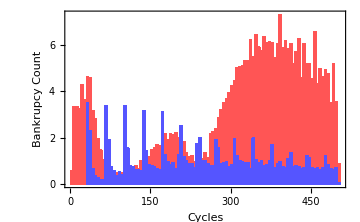
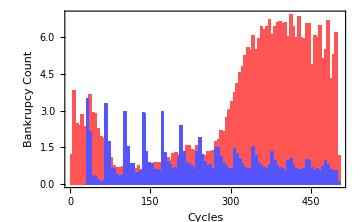

```mathematica
valuescons=Table[,{f,1,fl}];
valuescap=Table[,{f,1,fl}];
weightscons=Table[,{f,1,fl}];
weightscap=Table[,{f,1,fl}];
b=5;
Do[{valuescons[[f]],weightscons[[f]]}={dataf[[f,1,All,2]]+1,Mean[Table[dataf[[f,m,All,-1]],{m,1,nl[[f]]}]]},{f,1,fl}];
histcons=Table[WeightedHistogram[weightscons[[f]]->valuescons[[f]],{b},ChartStyle-> Lighter[Red],ImageSize-> 500],{f,1,fl}];
b=5;
Do[{valuescap[[f]],weightscap[[f]]}={dataf[[f,1,All,2]]+1,Mean[Table[dataf[[f,m,All,-2]],{m,1,nl[[f]]}]]},{f,1,fl}];
histcap=Table[WeightedHistogram[weightscap[[f]]->valuescap[[f]],{b}, ChartStyle-> Lighter[Blue],ImageSize-> 500],{f,1,fl}];
Table[Show[histcons[[f]],histcap[[f]],ImageSize->Medium,Frame-> True,FrameLabel->{"Cycles","Bankrupcy Count",info[[f]]", Red=Cons, Blue=Cap"},LabelStyle->15],{f,1,fl}]
```

### Employe1

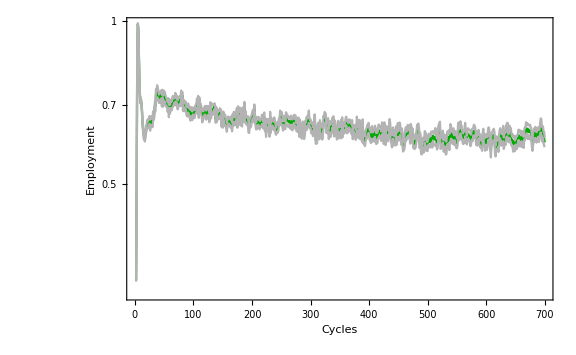
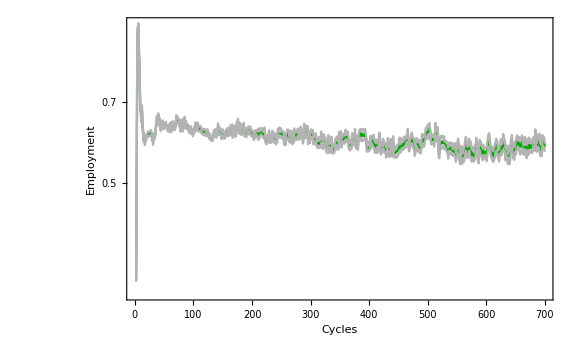
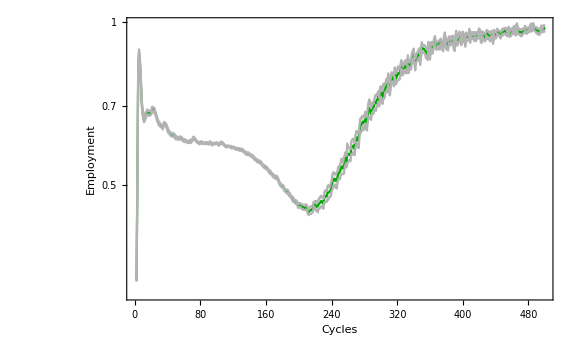
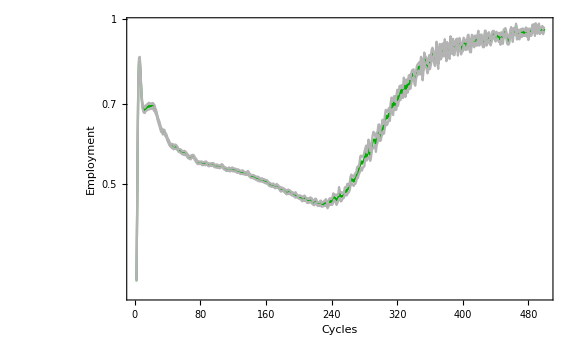

```mathematica
v=4;
plot1=Table[ListPlot[Transpose[{dataf[[f,1,All,2]],Table[Median[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot3=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Employment", info[[f]]},FrameStyle->15],{f,1,fl}]
```

### Consumption

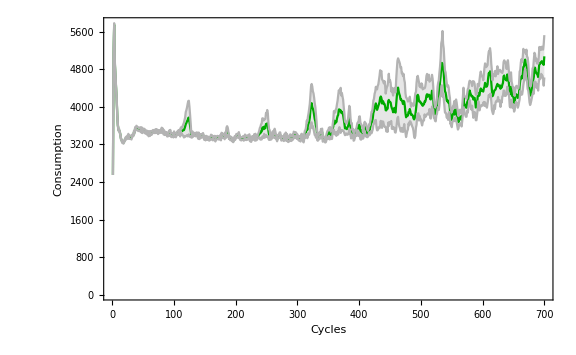
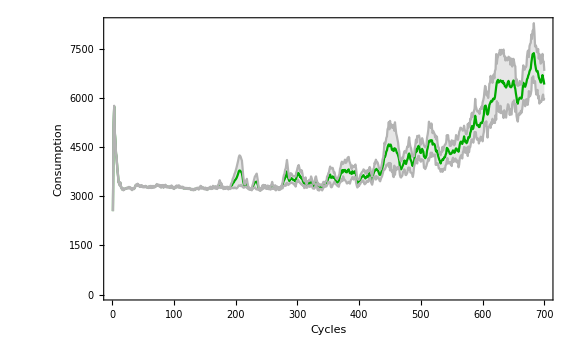
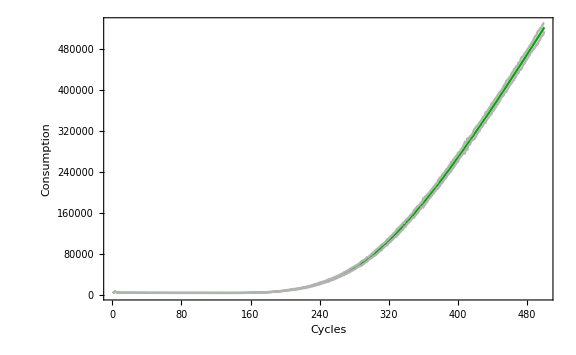
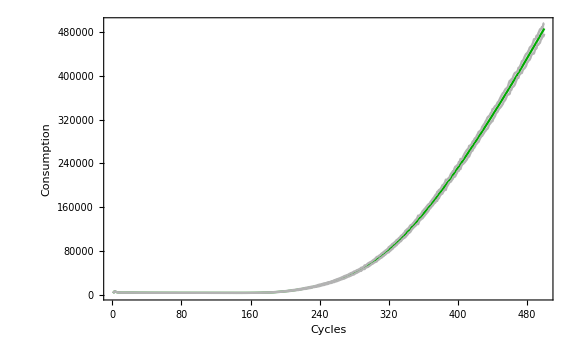

```mathematica
v=3;
plot1=Table[ListPlot[Transpose[{dataf[[f,1,All,2]],Table[Median[dataf[[f,All,m,v]]],{m,1,Length[data[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
Table[Show[plot2[[f]],plot2[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot3=Table[ListPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Consumption", info[[f]]},FrameStyle->15],{f,1,fl}]
```

### Fabricated Capital G

```mathematica
v=5;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot35=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Capital firms Output (Log)", info[[f]]},PlotLegends->{"Capital sector"},FrameStyle->15],{f,1,fl}];
```

### Fabricated Consumer G

```mathematica
v=6;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot36=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Red,GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Consumer firms Output (Log)", info[[f]]},PlotLegends->{"Consumer sector"},FrameStyle->15],{f,1,fl}];
```

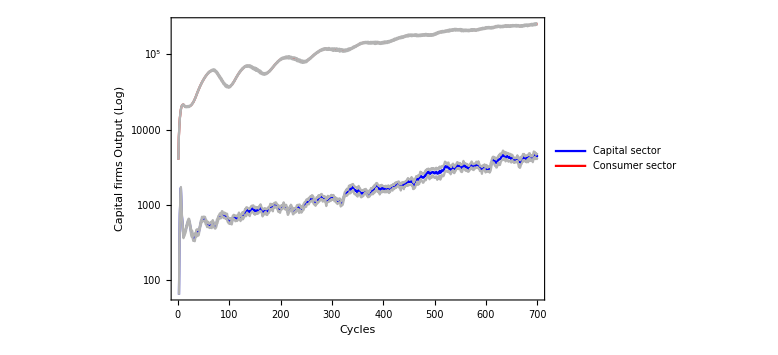
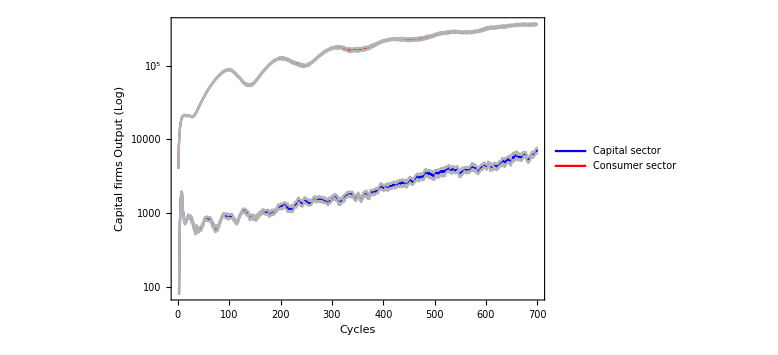
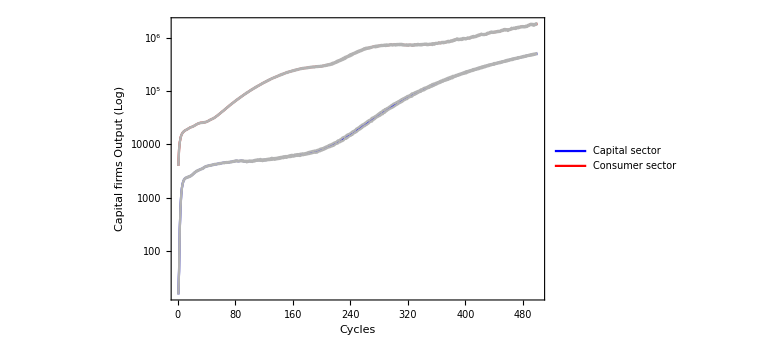
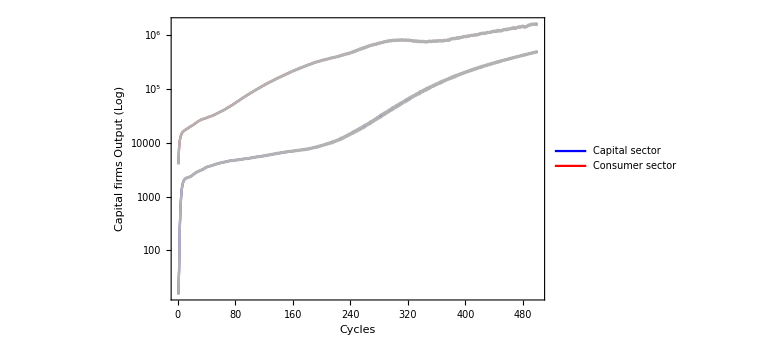

```mathematica
Table[Show[plot35[[f]],plot36[[f]],PlotRange->All],{f,1,fl}]
```

### Investment Capital G

```mathematica
v=7;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot37=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Capital firms investment (Log)", info[[f]]},PlotLegends->{"Capital sector"},FrameStyle->15],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
```

### Investment Consumer G

```mathematica
v=8;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot38=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Red,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Consumer firms investment (Log)", info[[f]]},PlotLegends->{"Consumer sector"},FrameStyle->15],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

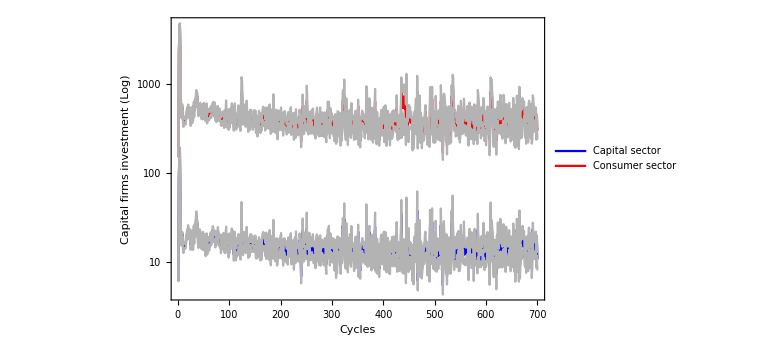
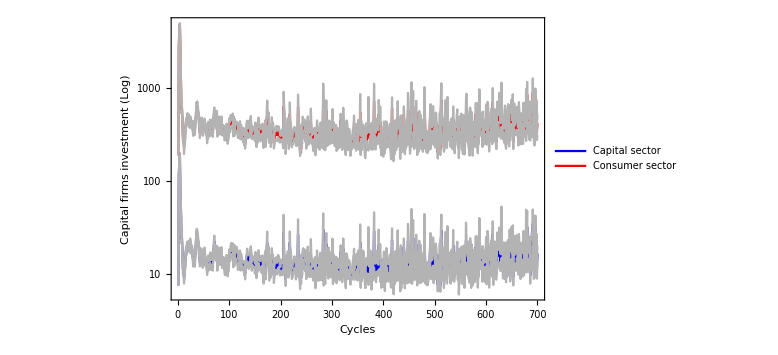
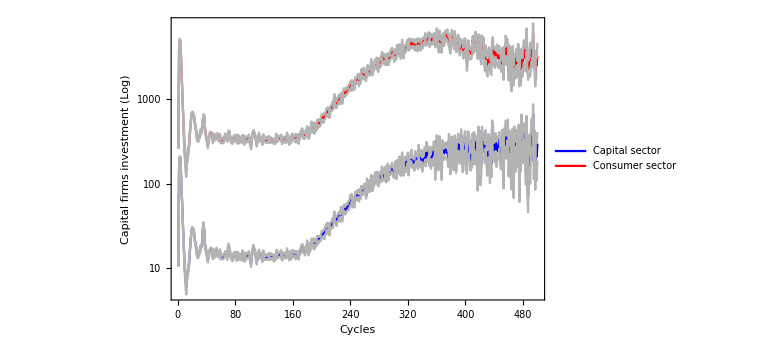
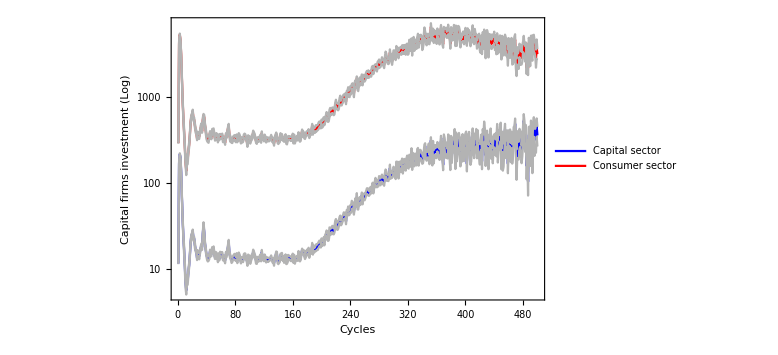

```mathematica
Table[Show[plot37[[f]],plot38[[f]],PlotRange->All],{f,1,fl}]
```

### Average productivity A (by Market shares)

```mathematica
v=9;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot39=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Red,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Productivity A", info[[f]]},FrameStyle->15],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

### Average productivity A (by labour)

```mathematica
v=10;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot310=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Red,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Productivity A", info[[f]]},FrameStyle->15],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

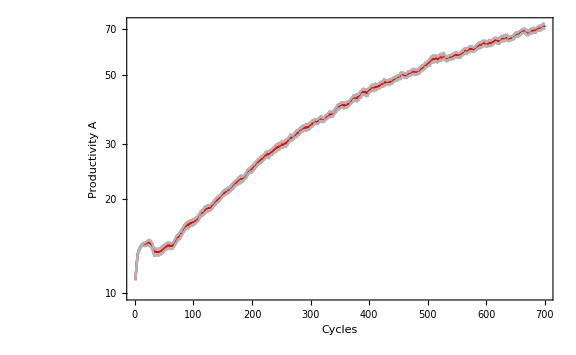
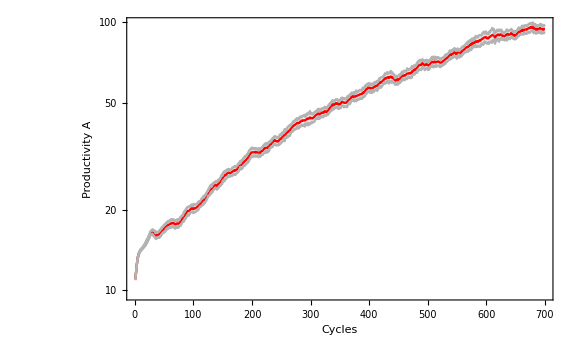
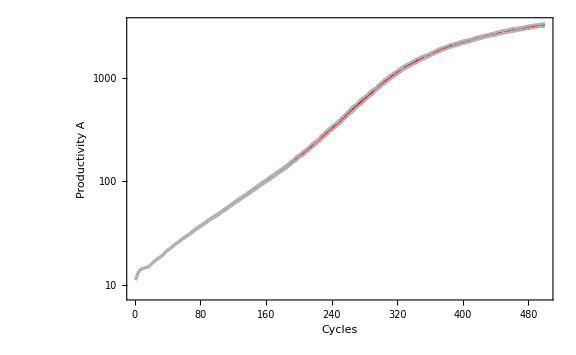
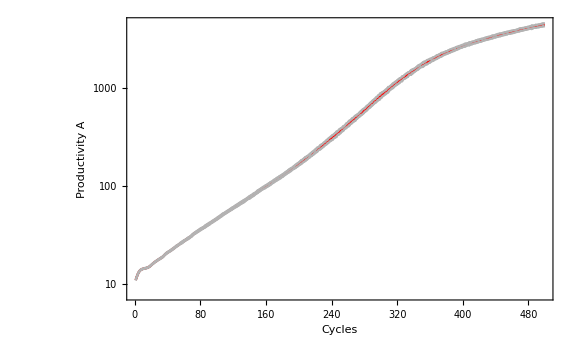

```mathematica
Table[Show[plot39[[f]],plot310[[f]]],{f,1,fl}]
```

### Average productivity B (by production/MS)

```mathematica
v=11;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot311=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Productivity B", info[[f]]},FrameStyle->15],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

### Average productivity B (by labour)

```mathematica
v=12;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot312=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","Productivity B", info[[f]]},FrameStyle->15],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

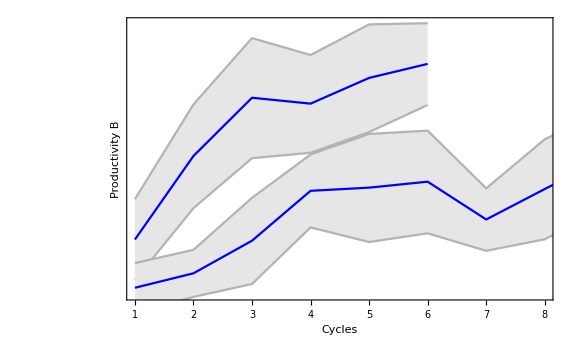
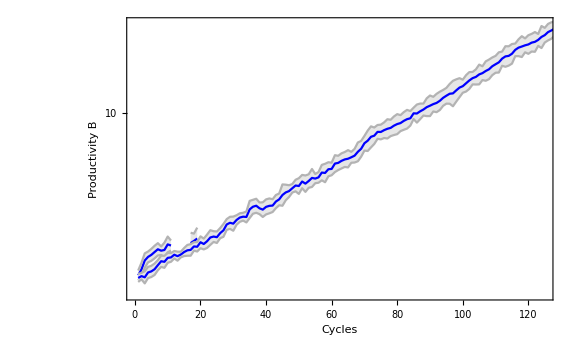
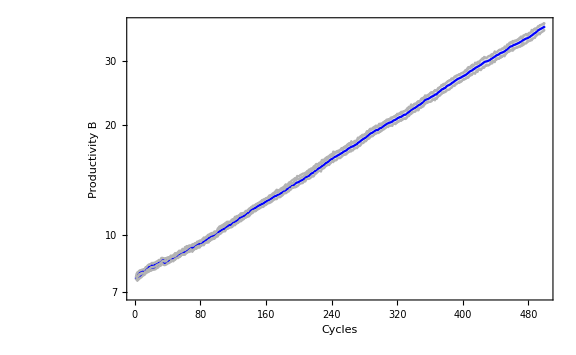
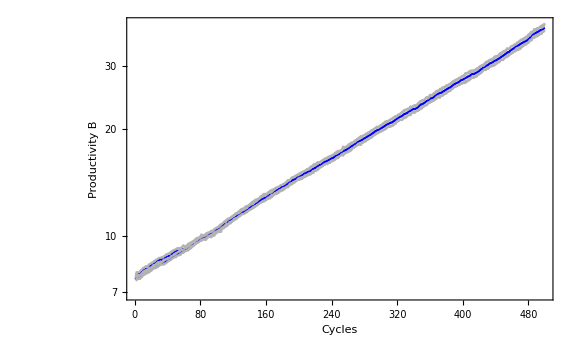

```mathematica
Table[Show[plot311[[f]],plot312[[f]]],{f,1,fl}]
```

### Employees in consumer sector

```mathematica
v=13;
plot1=Table[ListPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot313=Table[ListPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Red,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","# People", info[[f]]},FrameStyle->15,PlotLegends->{"Consumer sector"}],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

### Employees in capital sector

```mathematica
v=14;
plot1=Table[ListPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot314=Table[ListPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","# People", info[[f]]},FrameStyle->15,PlotLegends->{"Capital sector"}],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

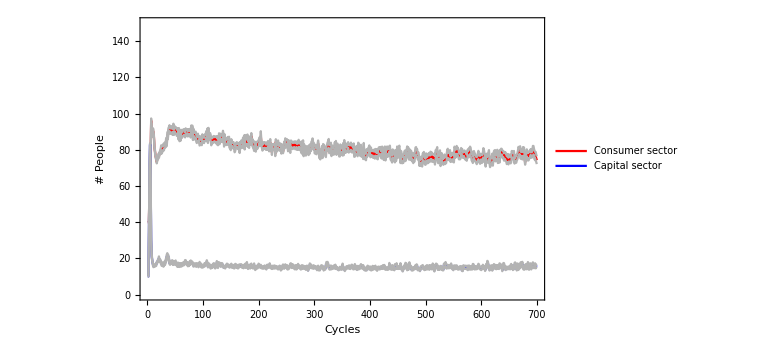
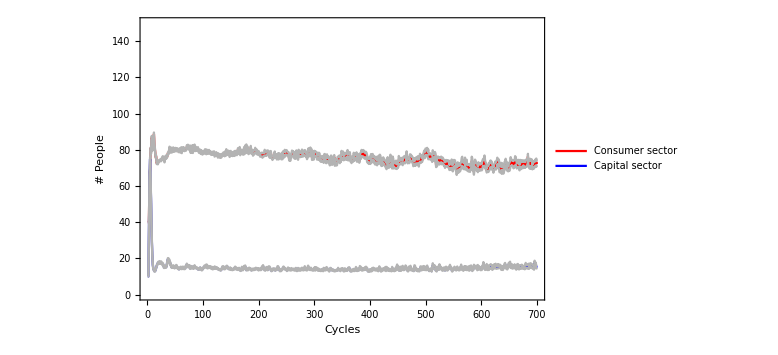
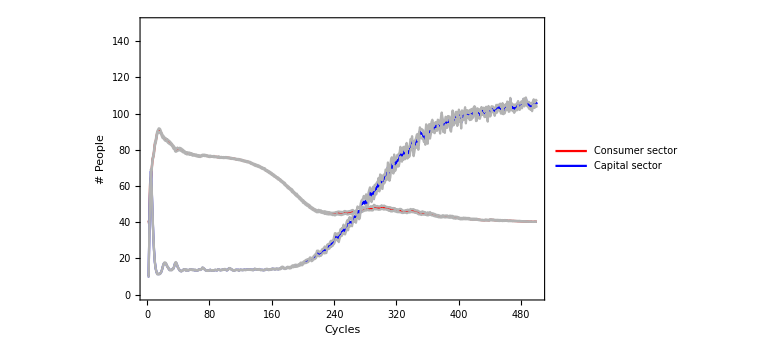
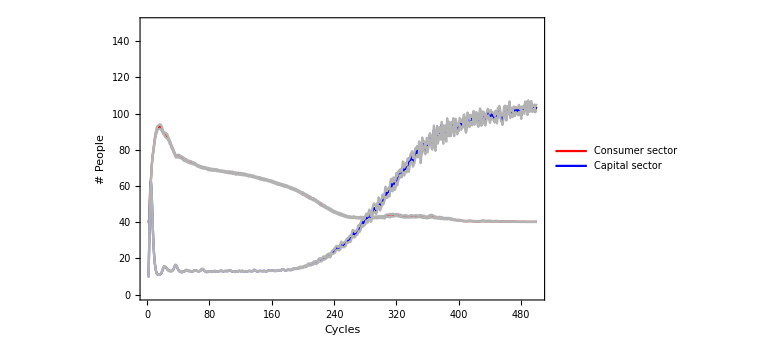

```mathematica
Table[Show[plot313[[f]],plot314[[f]],PlotRange->{All,{0,150}}],{f,1,fl}]
```

### CPI

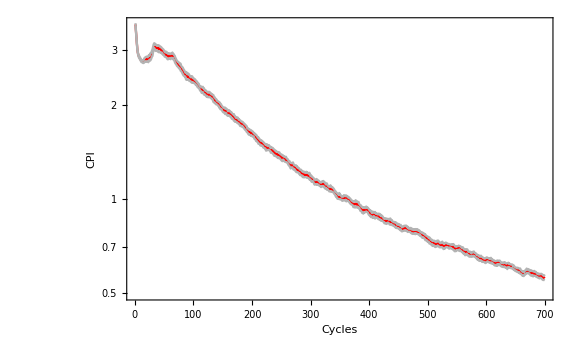
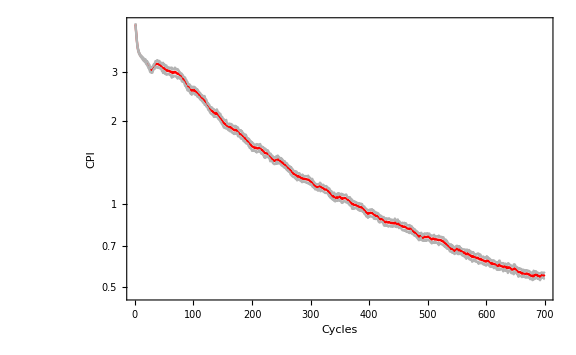
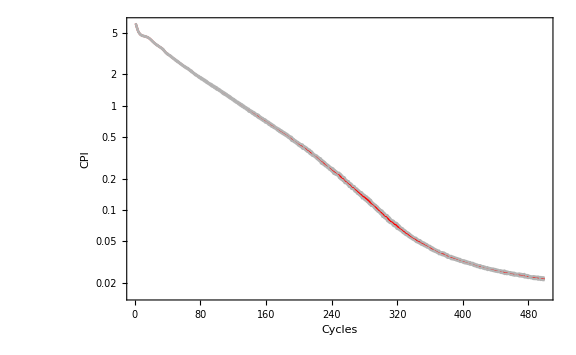
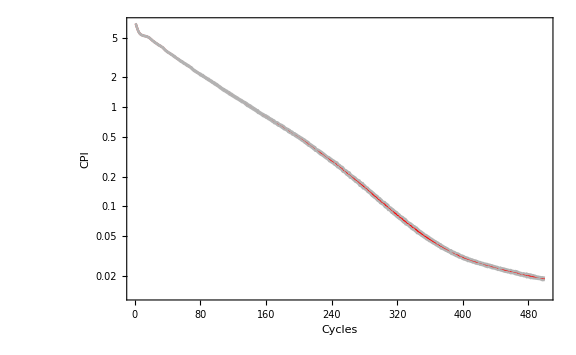

```mathematica
v=15;
plot1=Table[ListLogPlot[Transpose[{dataf[[f,1,All,2]],Table[Mean[dataf[[f,All,m,v]]],{m,1,Length[dataf[[f,1]]]}]}],Joined->True],{f,1,fl}];
plot2=Table[ListLogPlot[Table[Transpose[{dataf[[f,n,All,2]],dataf[[f,n,All,v]]}],{n,1,nl[[f]]}]],{f,1,fl}];
bootstraperr=Table[Table[StandardDeviation[Table[Mean[RandomSample[dataf[[f,All,j,v]],p[[f]]]],{i,1,20}]],{j,1,len[[f]]}],{f,1,fl}];
plot315=Table[ListLogPlot[{Mean[dataf[[f,All,All,v]]],Mean[dataf[[f,All,All,v]]]+bootstraperr[[f]],Mean[dataf[[f,All,All,v]]]-bootstraperr[[f]]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Red,GrayLevel[.7],GrayLevel[.7]},ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Blue,GrayLevel[.7],GrayLevel[.7]},PlotRange->All,ImageSize->Large,Joined->True,Filling->{2->{{3},GrayLevel[.9]}},PlotStyle->{Darker[Green],GrayLevel[.7],GrayLevel[.7]},Frame->True,FrameLabel->{"Cycles","CPI", info[[f]]},FrameStyle->15],{f,1,fl}]
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500],{f,1,fl}];
Table[Show[plot2[[f]],plot1[[f]],ImageSize->500,PlotRange->All],{f,1,fl}];
```

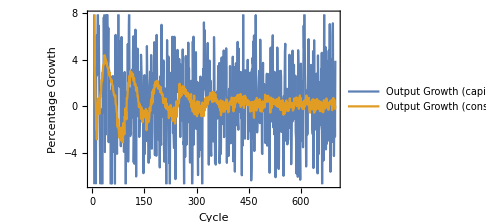
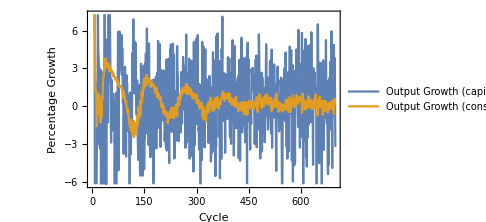
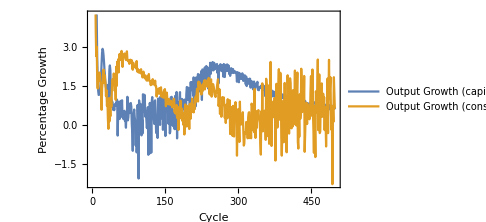
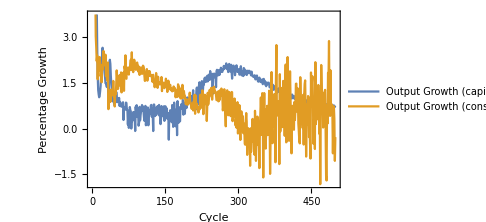

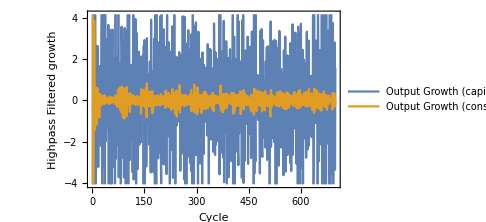
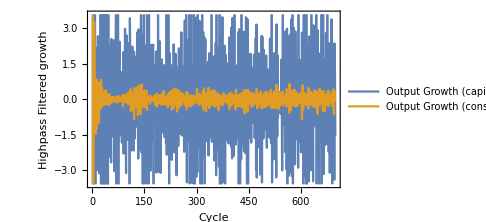
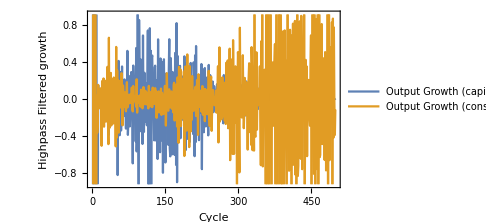
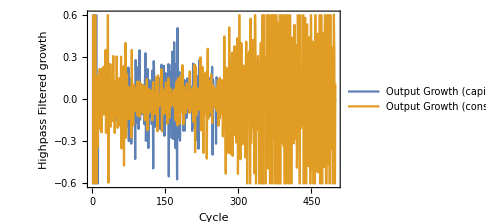

```mathematica
e=0.001;
Employ=Table[Table[Mean[dataf[[f,All,m,4]]],{m,1,Length[dataf[[f,1]]]}],{f,1,fl}]//N;
outCap=Table[Table[Mean[dataf[[f,All,m,5]]],{m,1,Length[dataf[[f,1]]]}],{f,1,fl}]//N;
outCons=Table[Table[Mean[dataf[[f,All,m,6]]],{m,1,Length[dataf[[f,1]]]}],{f,1,fl}]//N;
outinvCap=Table[Table[Mean[dataf[[f,All,m,7]]],{m,1,Length[dataf[[f,1]]]}],{f,1,fl}]//N;
outinvCons=Table[Table[Mean[dataf[[f,All,m,8]]],{m,1,Length[dataf[[f,1]]]}],{f,1,fl}]//N;
outinv=outinvCap+outinvCons;
cpi=Table[Table[Mean[dataf[[f,All,m,15]]],{m,1,Length[dataf[[f,1]]]}],{f,1,fl}]//N;
M=Table[Length[outCap[[f]]],{f,1,fl}];
outCapGrowth=Table[Table[100*(outCap[[f,m+1]]/outCap[[f,m]]-1),{m,1,M[[f]]-1}],{f,1,fl}];
outConsGrowth=Table[Table[100*(outCons[[f,m+1]]/outCons[[f,m]]-1),{m,1,M[[f]]-1}],{f,1,fl}];
outinvGrowth=Table[Table[100*(outinv[[f,m+1]]/(outinv[[f,m]]+e)-1),{m,1,M[[f]]-1}],{f,1,fl}];
inflation=Table[Table[100*(cpi[[f,m+1]]/cpi[[f,m]]-1),{m,1,M[[f]]-1}],{f,1,fl}];
EmployGrowth=Table[Table[100*(Employ[[f,m+1]]/Employ[[f,m]]-1),{m,1,M[[f]]-1}],{f,1,fl}];
Table[ListPlot[{outCapGrowth[[f]],outConsGrowth[[f]]},ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Cycle","Percentage Growth", info[[f]]},LabelStyle->Medium,PlotLegends->{"Output Growth (capital)","Output Growth (consumer)","Employment"}],{f,1,fl}]
Table[ListPlot[{HighpassFilter[outCapGrowth[[f]],1],HighpassFilter[outConsGrowth[[f]],1]},ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Cycle","Highpass Filtered growth", info[[f]]},LabelStyle->Medium,PlotLegends->{"Output Growth (capital)","Output Growth (consumer)","Investment Growth (capital)","Investment Growth (consumer)"}],{f,1,fl}]
Table[ListPlot[outinvGrowth[[f]],ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Cycle","Percentage Growth", info[[f]]},LabelStyle->Medium,PlotLegends->{"Investment Growth"}],{f,1,fl}]
Table[ListPlot[HighpassFilter[outinvGrowth[[f]],1],ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Cycle","Highpass Filtered growth", info[[f]]},LabelStyle->Medium,PlotLegends->{"Investment Growth"}],{f,1,fl}]
Table[ListPlot[inflation[[f]],ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Cycle","Percentage Growth", info[[f]]},LabelStyle->Medium,PlotLegends->{"Inflation"}],{f,1,fl}]
Table[ListPlot[HighpassFilter[inflation[[f]],1],ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Cycle","Highpass Filtered growth", info[[f]]},LabelStyle->Medium,PlotLegends->{"Inflation"}],{f,1,fl}]
```

```mathematica
f=2;
plot2=Manipulate[Row[ListLogPlot[{dataf[[f,n,All,5]],dataf[[f,n,All,6]],dataf[[f,n,All,7]],dataf[[f,n,All,8]],dataf[[f,n,All,3]]},ImageSize->Large,PlotRange->All,PlotMarkers->{Automatic},PlotLegends->{"Cap Fab","Cons Fab","Cap Inv","Cons Inv","Consumption"}],ListPlot[dataf[[f,n,All,4]],ImageSize->Large,PlotRange->{All,{0,1}}]],{n,1,nl[[f]],1}]
```

```mathematica
F[X_,μ_,σ_]:=D[PDF[UniformDistribution[{0,20}],X],X]
P[n_,μ_,σ_]:=Integrate[PDF[UniformDistribution[{0,40}],X],{X,0,n}]
```

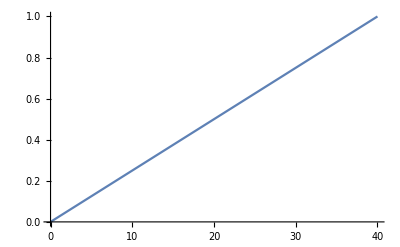

```mathematica
Plot[P[n,20,10],{n,0,40}]
```

```mathematica
3
```

3

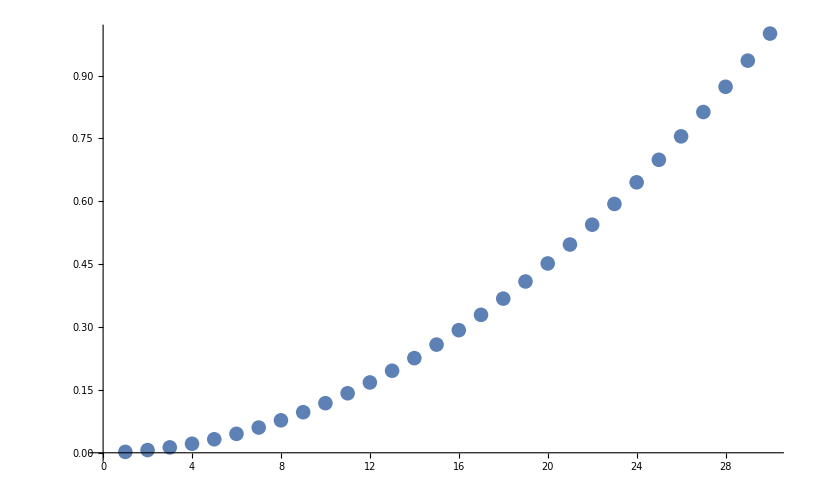

```mathematica
a=Table[Sum[P[n,20,10],{n,1,cyc}],{cyc,1,30}];
ListPlot[a/Max[a]]
```

```mathematica
a//N
```

{0.025,0.075,0.15,0.25,0.375,0.525,0.7,0.9,1.125,1.375,1.65,1.95,2.275,2.625,3.,3.4,3.825,4.275,4.75,5.25,5.775,6.325,6.9,7.5,8.125,8.775,9.45,10.15,10.875,11.625}

```mathematica
a={0.00656158147746766,0.014456597307557075,0.02386150504524577,0.03495358851319133,0.0479053480797805,0.06287809464335499,0.08001495384813573,0.09943355934645702,0.12121877704971208,0.14541584950162642,0.17202437449150187,0.20099352976765017,0.2322189231043263,0.2655413833935063,0.3007479160699362,0.33757493010026857,0.37571371164632095,0.4148179810438666,0.4545132357915677,0.4944074638317111,0.5341027185794122,0.5732069879769578,0.6113457695230102,0.6481727835533425,0.6833793162297724,0.7167017765189524,0.7479271698556286,0.7768963251317769,0.8035048501216523,0.8277019225735668};
```

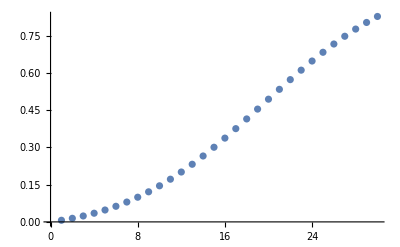

```mathematica
ListPlot[a]
```